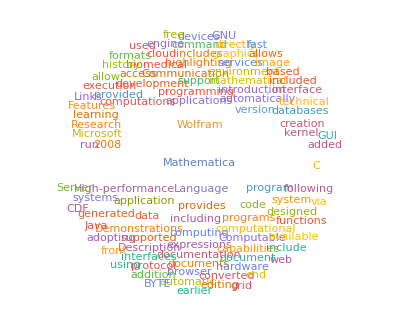

```mathematica
WordCloud[WikipediaData["Mathematica"]]
```

```mathematica
Crash Course in Mathematica for Graduate Students
```

## Introduction Lesson 2

In the previous lesson we played with calculus but MATHEMATICA is good also for doing linear algebra calculations which are common in physics.
We can define vector of elements simply doing

```mathematica
v= {1, 3, 5}
w = {2, 4, 6}
v+w
```

{1,3,5}

{2,4,6}

{3,7,11}

And also matrices

```mathematica
M = {{1, 3, 5}, {2, 5, 8}, {1, 4, 9}}//MatrixForm (*gives the Matrix-like output*)
```

(1 | 3 | 5
2 | 5 | 8
1 | 4 | 9)

Obviously all the standard operation between vector and matrices are allowed,  but only in the ‘original version’.

```mathematica
v={1, 2, 3}//MatrixForm
M.v
```

(1
2
3)

(1 | 3 | 5
2 | 5 | 8
1 | 4 | 9).(1
2
3)

```mathematica
M = {{1, 3, 5}, {2, 5, 8}, {1, 4, 9}};
v={1, 2, 3}
M.v
M.v//MatrixForm
```

{1,2,3}

{22,36,36}

(22
36
36)

Matrices and vectors are lists for MATHEMATICA. We have access to their elements simply

```mathematica
M[[1]] (*first row*)
```

{1,3,5}

```mathematica
M[[1, 3]](*first row but also third column*)
M[[1]][[ 3]](*but the meaning of this is slightly different*)
```

5

5

```mathematica
M[[All , 3]](*only the third column*)
```

{5,8,9}

Lists are more general object. For more info see [4].

## Current in DC Circuit

Consider the DC circuit in the picture above. Use Kirchoff’s Laws to determine the currents i_1, i_2 and i_3 in terms of V, R_1, R_2 and R_3.
Kirchoff’s node and loops lwas give us the following equations:

We can define the equations

```mathematica
eq1 = i1 == i2 + i3;
eq2 = V == i1 R1 + i2 R2;
eq3 = 0 == i2 R2 - i3 R3;
eq4 = V == i1 R1 + i3 R3;
```

And solve them

```mathematica
Solve[{eq1, eq2, eq3}, {i1, i2, i3}]
```

{{i1→((R2+R3) V)/(R1 R2+R1 R3+R2 R3),i2→(R3 V)/(R1 R2+R1 R3+R2 R3),i3→(R2 V)/(R1 R2+R1 R3+R2 R3)}}

They correspond to this matrix.

```mathematica
M={{-1, 1, 1},{R1, R2, 0},{0, R2, -R3}}//Transpose;
{{-1, 1, 1},{R1, R2, 0},{0, R2, -R3}}//Transpose//MatrixForm
```

(-1 | R1 | 0
1 | R2 | R2
1 | 0 | -R3)

with these homogeneous part

```mathematica
v={0, V, 0};
{0, V, 0}//MatrixForm
```

(0
V
0)

```mathematica
LinearSolve[M, v]
```

{(R1 R3 V)/(R1 R2+R1 R3+R2 R3),(R3 V)/(R1 R2+R1 R3+R2 R3),(R1 V)/(R1 R2+R1 R3+R2 R3)}

## Special Relativity and Boosted Objects

If we define the Lorentzian metric as the matrix

```mathematica
g=DiagonalMatrix[{1, -1, -1, -1}];
%//MatrixForm
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

we can use it to compute scalar product in Minkowski space.

```mathematica
v1= {1, 0, 0, 1};
v2={1, 0, 0, -1};
v2.g.v1 (*this is the same than the Dot[] function*)
```

2

Consider a pion ( π ) at rest which decays into two photons ( γ ).  In the rest frame of the pion the μ and the ν will decay in a back-to-back configuration.

Thus the 4-vectors are

```mathematica
Subscript[p, π]={m0, 0, 0, 0};  (*Rest frame 4-vectors*)
p1={ω, 0, 0, ω};
p2={ω, 0, 0, -ω};
```

```mathematica
a=Part[p1,2;;4];
b=Part[p2, 2;;4];
ma=Sqrt[Transpose[a].a];
mb=Sqrt[Transpose[b].b];
Solve[Transpose@a.b == Cos[α] ma mb, Cos[α]]
```

{{Cos[α]→-1}}

Compute how the angle between the two photons varies in a generic boosted frame in the x directions. Plot θ(β).

```mathematica
γ=1/(√(1-β^2));
Λ={{γ, -γ β, 0, 0},{-γ β,γ, 0, 0},{0, 0, 1, 0},{0, 0, 0, 1}}; (*Lorenz transformation*)
{{γ, -γ β, 0, 0},{-γ β,γ, 0, 0},{0, 0, 1, 0},{0, 0, 0, 1}}//MatrixForm
```

(1/(√(1-β^2)) | -β/(√(1-β^2)) | 0 | 0
-β/(√(1-β^2)) | 1/(√(1-β^2)) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Subscript[pulse, π]=Part[Λ.Subscript[p, π], 2;;4] (*the same than the [[]] command*)
pulse1=Part[Λ.p1, 2;;4]
pulse2=Part[Λ.p2, 2;;4]
```

{-(m0 β)/(√(1-β^2)),0,0}

{-(β ω)/(√(1-β^2)),0,ω}

{-(β ω)/(√(1-β^2)),0,-ω}

```mathematica
mod1=Sqrt[Transpose[pulse1].pulse1];
mod2=Sqrt[Transpose[pulse2].pulse2];
mod1 mod2 Cos[θ]==Transpose[pulse1].pulse2 /.ω->m0/2
Simplify@Solve[%,Cos[θ]]
```

(m0^2/4+(m0^2 β^2)/(4 (1-β^2))) Cos[θ]==-m0^2/4+(m0^2 β^2)/(4 (1-β^2))

{{Cos[θ]→-1+2 β^2}}

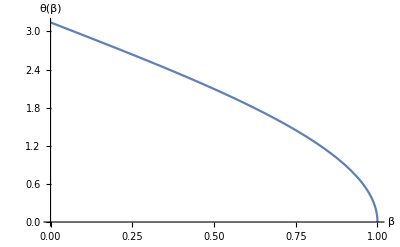

```mathematica
Plot[ArcCos[-1+2 β^2], {β, 0, 1}, AxesLabel->{β, "θ(β)"}]
```

## Inertia Tensor and Principal Axes

The most general notion of moment of inertia is encoded in the inertia tensor.

Measured in the body frame  is a constant real symmetric matrix, hence it admits a decomposition into a rotation matrix  and a diagonal matrix  such that

Columns of the rotation matrix  define the directions of the principal axes of the body. If  the scalar  and  are called principal moments of inertia.
Given the mass distribution below compute the inertia tensor for this body and find its principal axes/moments.

```mathematica
Ω=Cylinder[{{0,0,0},{1,1,1}},1/2]; (*A cylinder from the origin to {1,1,1} with radius 1/2:*)
Graphics3D[Ω]
```

-Graphics3D-

```mathematica
V=Integrate[1, Element[X, Ω]] (*Volume of the ellipsoid*)
cm=1/V Integrate[X, Element[X, Ω]] (*center of mass*)
```

(√3 π)/4

{1/2,1/2,1/2}

```mathematica
(*between X and {r, θ, z} there are intermidiate coordinates X'=RX*)
```

```mathematica
R=RotationMatrix[{{0, 0, 1}, {1, 1, 1}}]; (*rotates the first vector in the second one*)
%//MatrixForm
```

(1/6 (3+√3) | 1/6 (-3+√3) | 1/(√3)
1/6 (-3+√3) | 1/6 (3+√3) | 1/(√3)
-1/(√3) | -1/(√3) | 1/(√3))

```mathematica
X={x, y, z};
X2=R.X-cm;
m=Dot[X2,X2]IdentityMatrix[3]-Outer[Times, X2, X2]/.{x->r Cos[θ], y->r Sin[θ]}//FullSimplify;
%//MatrixForm (*inertia tensor in cylindrical coordinates*)
```

(1/36 ((-3+2 √3 z+(-3+√3) r Cos[θ]+(3+√3) r Sin[θ])^2+(3-2 √3 z+2 √3 r (Cos[θ]+Sin[θ]))^2) | 1/12 (-3+4 √3 z-4 z^2+2 r (√3-2 z) (Cos[θ]+Sin[θ])+2 r^2 (1-4 Cos[θ] Sin[θ])) | -1/36 (-3+2 √3 z+(3+√3) r Cos[θ]+(-3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ]))
1/12 (-3+4 √3 z-4 z^2+2 r (√3-2 z) (Cos[θ]+Sin[θ])+2 r^2 (1-4 Cos[θ] Sin[θ])) | 1/36 ((-3+2 √3 z+(3+√3) r Cos[θ]+(-3+√3) r Sin[θ])^2+(3-2 √3 z+2 √3 r (Cos[θ]+Sin[θ]))^2) | -1/36 (-3+2 √3 z+(-3+√3) r Cos[θ]+(3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ]))
-1/36 (-3+2 √3 z+(3+√3) r Cos[θ]+(-3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ])) | -1/36 (-3+2 √3 z+(-3+√3) r Cos[θ]+(3+√3) r Sin[θ]) (-3+2 √3 z-2 √3 r (Cos[θ]+Sin[θ])) | 1/6 (3-4 √3 z+4 z^2-2 r (√3-2 z) (Cos[θ]+Sin[θ])-2 r^2 (-2+Sin[2 θ])))

```mathematica
Inertia=MomentOfInertia[Ω]; (*compute it for our rotated cylinder it would not have been easy*)
%//MatrixForm  (*if not specified it computes the inertia tensor wrt the cm*)
```

((√3 π)/16 | -(√3 π)/64 | -(√3 π)/64
-(√3 π)/64 | (√3 π)/16 | -(√3 π)/64
-(√3 π)/64 | -(√3 π)/64 | (√3 π)/16)

```mathematica
P=Transpose@Eigenvectors[Inertia];
%//MatrixForm
Eigenvalues[Inertia]
```

(-1 | -1 | 1
0 | 1 | 1
1 | 0 | 1)

{(5 √3 π)/64,(5 √3 π)/64,(√3 π)/32}

Let me check they are eigenvectors

```mathematica
Table[v=P[[All, i]];
Solve[Inertia.v== λ v, λ], {i, 1, 3}]
```

{{{λ→(5 √3 π)/64}},{{λ→(5 √3 π)/64}},{{λ→(√3 π)/32}}}

```mathematica
Inverse[P].Inertia.P//FullSimplify;
%//MatrixForm (*which is diagonal*)
```

((5 √3 π)/64 | 0 | 0
0 | (5 √3 π)/64 | 0
0 | 0 | (√3 π)/32)

Adding the jacobian we can also use the inertia tensor definition to obtain the same result.

```mathematica
Inertia2=Integrate[m*r, {r, 0, 1/2},{θ, -Pi, Pi},{z, 0, Sqrt[3]}];(*they are the same!*)
%//MatrixForm
```

((√3 π)/16 | -(√3 π)/64 | -(√3 π)/64
-(√3 π)/64 | (√3 π)/16 | -(√3 π)/64
-(√3 π)/64 | -(√3 π)/64 | (√3 π)/16)

## Eigenmodes of the Heat Equation

The Heat Equation is

Using the DEigensystem function we can easily find heat equation smallest eigenfunctions and eigenvalues.

```mathematica
Nmax=20;
{ℒ,ℬ}={D[u[t,x],t]==Laplacian[u[t,x],{x}],DirichletCondition[u[t,x]==0,True]};
{vals,funs}=DEigensystem[{ℒ,ℬ},u[t,x],t,{x,0,1},Nmax]
```

{{-π^2,-4 π^2,-9 π^2,-16 π^2,-25 π^2,-36 π^2,-49 π^2,-64 π^2,-81 π^2,-100 π^2,-121 π^2,-144 π^2,-169 π^2,-196 π^2,-225 π^2,-256 π^2,-289 π^2,-324 π^2,-361 π^2,-400 π^2},{ⅇ^(-π^2 t) Sin[π x],ⅇ^(-4 π^2 t) Sin[2 π x],ⅇ^(-9 π^2 t) Sin[3 π x],ⅇ^(-16 π^2 t) Sin[4 π x],ⅇ^(-25 π^2 t) Sin[5 π x],ⅇ^(-36 π^2 t) Sin[6 π x],ⅇ^(-49 π^2 t) Sin[7 π x],ⅇ^(-64 π^2 t) Sin[8 π x],ⅇ^(-81 π^2 t) Sin[9 π x],ⅇ^(-100 π^2 t) Sin[10 π x],ⅇ^(-121 π^2 t) Sin[11 π x],ⅇ^(-144 π^2 t) Sin[12 π x],ⅇ^(-169 π^2 t) Sin[13 π x],ⅇ^(-196 π^2 t) Sin[14 π x],ⅇ^(-225 π^2 t) Sin[15 π x],ⅇ^(-256 π^2 t) Sin[16 π x],ⅇ^(-289 π^2 t) Sin[17 π x],ⅇ^(-324 π^2 t) Sin[18 π x],ⅇ^(-361 π^2 t) Sin[19 π x],ⅇ^(-400 π^2 t) Sin[20 π x]}}

We can plot them and notice that they are damped from the time exponential.

```mathematica
Table[Plot3D[funs[[i]],{x,-1,1},{t,0,0.2},PlotRange->All,Ticks->False,Mesh->False],{i,Nmax}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*It is possible to decompose an arbitrary function on the eigenfunction base and study the evolution of the system with this as an initial condition?*)
```

```mathematica
Code Here
```

```mathematica
L2norm[f1_, f2_, Domain_:{x, 0, 1}]:=Module[{},
Integrate[Conjugate[f2]*f1, Domain]
]
```

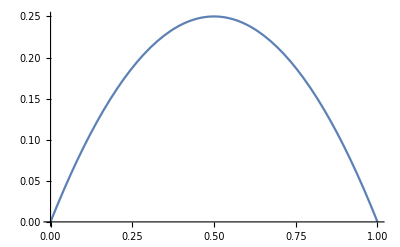

```mathematica
f[x_]=x(1-x); (*our function*)
Plot[%, {x, 0, 1}]
```

```mathematica
coeff[t_]=Table[L2norm[f[x], funs[[i]]], {i, 1, Nmax}] (*the coefficient on the eigenfunction bases*)
```

{(4 ⅇ^(-π^2 Conjugate[t]))/π^3,0,(4 ⅇ^(-9 π^2 Conjugate[t]))/(27 π^3),0,(4 ⅇ^(-25 π^2 Conjugate[t]))/(125 π^3),0,(4 ⅇ^(-49 π^2 Conjugate[t]))/(343 π^3),0,(4 ⅇ^(-81 π^2 Conjugate[t]))/(729 π^3),0,(4 ⅇ^(-121 π^2 Conjugate[t]))/(1331 π^3),0,(4 ⅇ^(-169 π^2 Conjugate[t]))/(2197 π^3),0,(4 ⅇ^(-225 π^2 Conjugate[t]))/(3375 π^3),0,(4 ⅇ^(-289 π^2 Conjugate[t]))/(4913 π^3),0,(4 ⅇ^(-361 π^2 Conjugate[t]))/(6859 π^3),0}

```mathematica
expr[t_, x_]=Sum[coeff[0][[i]]*funs[[i]], {i, 1, Nmax}] (*the expansion*)
```

(4 ⅇ^(-π^2 t) Sin[π x])/π^3+(4 ⅇ^(-9 π^2 t) Sin[3 π x])/(27 π^3)+(4 ⅇ^(-25 π^2 t) Sin[5 π x])/(125 π^3)+(4 ⅇ^(-49 π^2 t) Sin[7 π x])/(343 π^3)+(4 ⅇ^(-81 π^2 t) Sin[9 π x])/(729 π^3)+(4 ⅇ^(-121 π^2 t) Sin[11 π x])/(1331 π^3)+(4 ⅇ^(-169 π^2 t) Sin[13 π x])/(2197 π^3)+(4 ⅇ^(-225 π^2 t) Sin[15 π x])/(3375 π^3)+(4 ⅇ^(-289 π^2 t) Sin[17 π x])/(4913 π^3)+(4 ⅇ^(-361 π^2 t) Sin[19 π x])/(6859 π^3)

```mathematica
Plot3D[expr[t, x], {x, 0, 1}, {t, 0, 0.5}, PlotRange->All, Mesh->False, Ticks->False]
```

-Graphics3D-

## References

[1] A Mathematica Primer for Physicists, Jim Napolitano
[2] https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
[3] https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
[4] https://reference.wolfram.com/language/tutorial/Lists.html#2534
[5] https://demonstrations.wolfram.com/2DWavePropagation/
[6] https://mathematica.stackexchange.com/questions/134609/why-should-i-avoid-the-for-loop-in-mathematica
[7] https://reference.wolfram.com/language/ref/Module.html